```mathematica
(* Error arising from discretisting at the i^th time point, an integral of the product of terms before (i-1)/n*)
```

```mathematica
f1[n_,k_,a_,g_]:=(1 - Exp[(-2 n)/(k-1)a (g-x)])PDF[NormalDistribution[0,√((k-1)/n)],x](g-x)PDF[NormalDistribution[0,1/(√n)],x - g]
```

```mathematica
(* Survival probability of BM under a linear boundary a + bt. Used in the second error term *)
```

```mathematica
survivalprob[a_,b_,T_]:=CDF[NormalDistribution[],b √T + a/(√T)] - ⅇ^(- a b)CDF[NormalDistribution[],b √T -a/(√T)]
```

```mathematica
(* Error arising from discretisting at the i^th time point, an integral of the product of terms after (i+1)/n*)
```

```mathematica
f2[n_,k_,a_,g_]:= survivalprob[g-x, 1, 1 - (k+1)/n](g-x)PDF[NormalDistribution[0,1/(√n)],x-g]
```

```mathematica
(* Table of errors from k = 1 to n*)
```

```mathematica
nlist[N1_,N2_,δ_] := Table[
NIntegrate[f1[n,n,1,1],{x,-∞,1}]+
NIntegrate[f2[n,1,1,1],{x,-∞,1}]+
Total[
Table[
NIntegrate[f1[n,k,1,1],{x,-∞,1}]*
NIntegrate[f2[n,k,1,1],{x,-∞,1}],{k,2,n-2}]],
{n,N1,N2,δ}]
```

```mathematica
nlist[10,20,1]
```

{0.0971403,0.0892806,0.0826047,0.0768657,0.0718806,0.0675107,0.0636491,0.0602122,0.0571335,0.0543598,0.0518478}

```mathematica
(* Convergence plot of ∑_(k=1)^n Subscript[Error, k]. It looks like 1/n, which is what we need. *)
```

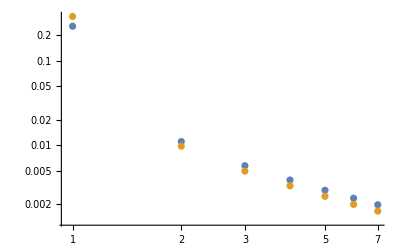

```mathematica
ListLogLogPlot[{nlist[3,700,100],Table[1/n,{n,3,700,100}]}]
```

```mathematica
(* f[y] is the integrand where we want to take partial derivatives for the EMSF*)
```

```mathematica
f[y_]:=(1 - Exp[-2 n(Subscript[g, i+1]-Subscript[x, i+1])(Subscript[g, i]-y)])PDF[NormalDistribution[0,1/(√n)],Subscript[x, i+1]-y]*(1 - Exp[-2 n(Subscript[g, i]-y)(Subscript[g, i-1]-Subscript[x, i-1])])PDF[NormalDistribution[0,1/(√n)],Subscript[x, i-1]-y]
```

```mathematica
(* First Partial derivative is 0 *)
```

```mathematica
Evaluate[D[f[y],{y,1}]]/. y-> Subscript[g, i]
```

0

```mathematica
(* Second partial derivative is skipped in the EMSF, because it is multiplied by the Bernoulli number Subscript[B, 3] = 0. Since the Bernoulli numbers Subscript[B, n] are 0 for all odd n, we skip all the even order partial derivatives. *)
```

```mathematica
Evaluate[D[f[y],{y,2}]]/. y-> Subscript[g, i]//FullSimplify
```

(4 ⅇ^(-1/2 n ((g_i-x_(-1+i))^2+(g_i-x_(1+i))^2)) n^3 (-g_(-1+i)+x_(-1+i)) (-g_(1+i)+x_(1+i)))/π

```mathematica
(* Third partial derivatives depends on the second derivative through the (Subscript[g, -1+i]-2 Subscript[g, i]+Subscript[g, 1+i]) term*)
```

```mathematica
Evaluate[D[f[y],{y,3}]]/. y-> Subscript[g, i] //FullSimplify
```

(12 ⅇ^(-1/2 n ((g_i-x_(-1+i))^2+(g_i-x_(1+i))^2)) n^4 (g_(-1+i)-2 g_i+g_(1+i)) (-g_(-1+i)+x_(-1+i)) (-g_(1+i)+x_(1+i)))/π

```mathematica
(* Third partial derivative is zero for linear boundaries, because the (Subscript[g, -1+i]-2 Subscript[g, i]+Subscript[g, 1+i]) term is a finite difference approximation of the second derivative. *)
```

```mathematica
Evaluate[D[f[y],{y,3}]]/. y-> Subscript[g, i] /. Subscript[g, i+1]-> Subscript[g, i] + K/n /. Subscript[g, i-1]-> Subscript[g, i] - K/n //FullSimplify
```

0

```mathematica
(* In fact it appears that the odd derivatives zero whenever the boundaries a linear. This implies that the residual error must be Exponential *)
```

```mathematica
Table[Evaluate[D[f[y],{y,M}]]/. y-> Subscript[g, i] /. Subscript[g, i+1]-> Subscript[g, i] + K/n /. Subscript[g, i-1]-> Subscript[g, i] - K/n //FullSimplify ,{M,1,15,2}]
```

{0,0,0,0,0,0,0,0}

```mathematica
(*_________________________________________________________________________________Now we investigate how to bound the integrals __________________________________________________________________________*)
```

```mathematica
(* Bounding Subscript[ϕ, (k-1)/n][x] by √(n/(2π(k-1)))*)
```

```mathematica
f1a[n_,k_,a_,g_]:=(1 - Exp[(-2 n)/(k-1)a (g-x)]) √(n/(2 π (k-1)))(g-x)PDF[NormalDistribution[0,1/(√n)],x - g]
```

```mathematica
nlista[N1_,N2_,δ_] := Table[
Total[
Table[
NIntegrate[f1a[n,k,1,1],{x,-∞,1}]*
NIntegrate[f2[n,k,1,1],{x,-∞,1}],{k,2,n-2}]],
{n,N1,N2,δ}]
```

```mathematica
(*Bounding Subscript[ϕ, (k-1)/n][x] by √(n/(2π(k-1))) reduces convergence rate to 1/√n. This implies that the exponential term in the pdf makes a difference. *)
```

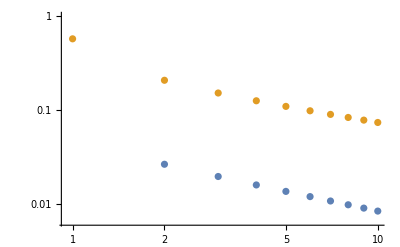

```mathematica
ListLogLogPlot[{nlista[3,200,20],Table[1/(√n),{n,3,200,20}]}]
```

```mathematica
f1b[n_,k_,a_,g_]:=(1 - Exp[(-2 n)/(k-1)a (g-x)])PDF[NormalDistribution[0,√((k-1)/n)],x](g-x)√(n/(2π))
```

```mathematica
nlistb[N1_,N2_,δ_] := Table[
Total[
Table[
NIntegrate[f1b[n,k,1,1],{x,-∞,1}]*
NIntegrate[f2[n,k,1,1],{x,-∞,1}],{k,2,n-2}]],
{n,N1,N2,δ}]
```

```mathematica
(* Removing last term loses convergence completely!*)
```

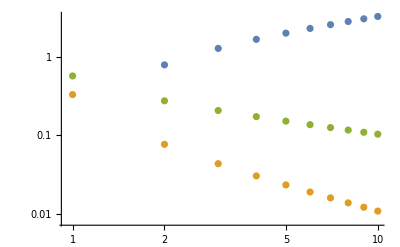

```mathematica
ListLogLogPlot[{nlistb[3,100,10],Table[1/n,{n,3,100,10}],Table[1/(√n),{n,3,100,10}]}]
```

```mathematica
f1c[n_,k_,a_,g_]:=(2 n)/(k-1)a (g-x)PDF[NormalDistribution[0,√((k-1)/n)],x](g-x)PDF[NormalDistribution[0,1/(√n)],x - g]
```

```mathematica
nlistc[N1_,N2_,δ_] := Table[
Total[
Table[
NIntegrate[f1c[n,k,1,1],{x,-∞,1}]*
NIntegrate[f2[n,k,1,1],{x,-∞,1}],{k,2,n-2}]],
{n,N1,N2,δ}]
```

```mathematica
(* It appears that replacing BB correction with the term in the exponent retains the convergence rate*)
```

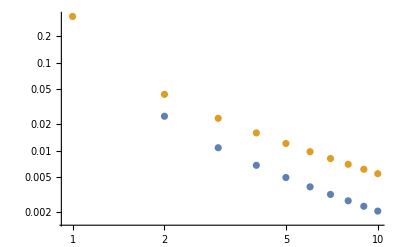

```mathematica
ListLogLogPlot[{nlistc[3,200,20],Table[1/n,{n,3,200,20}]}]
```

```mathematica
∫_(-∞)^g (g-x)^2 PDF[NormalDistribution[0,√((k-1)/n)],x]PDF[NormalDistribution[0,1/(√n)],x - g]ⅆx
```

ConditionalExpression[1/(4 k^3 √((-1+k)/n) √n √((g^2 n)/((-1+k) k)) √((g^2 (-1+k) n)/k) √((k n)/(-1+k)) π)ⅇ^(-g^2 n) ((2 ⅇ^((g^2 (-1+2 k) n)/(2 k)) (-1+k)^(5/2) k^(5/2) ((g^2 n)/((-1+k) k))^(3/2) √((g^2 (-1+k) n)/k) √((k n)/(-1+k)) √(2 π) Erf[(g √((-1+k)/k) √n)/(√2)])/(√n)+ⅇ^((g^2 (-1+2 k) n)/(2 k)) g √((g^2 (-1+k) n)/k) √((k n)/(-1+k)) (-k+k^2+g^2 n) √(2 π) Erf[(√((g^2 n)/((-1+k) k)))/(√2)]-k √((g^2 n)/((-1+k) k)) (-√((g^2 (-1+k) n)/k) ((2 ⅇ^((g^2 (-3+2 k) n)/(2 (-1+k))) g k n)/(√((k n)/(-1+k)))+ⅇ^((g^2 (-1+2 k) n)/(2 k)) (-k+k^2+g^2 n) √(2 π))+2 ⅇ^((g^2 (-1+2 k) n)/(2 k)) g^3 (-1+k)^2 n √((k n)/(-1+k)) √(2 π) Erf[(√((g^2 (-1+k) n)/k))/(√2)])),(Re[(k n)/(-1+k)]==0&&Re[g n]<0)||(Re[(k n)/(-1+k)]≥0&&Re[(k n)/(1-k)]<0)]

```mathematica
1/(4 k^3 √((-1+k)/n) √n √((g^2 n)/((-1+k) k)) √((g^2 (-1+k) n)/k) √((k n)/(-1+k)) π)ⅇ^(-g^2 n) ((2 ⅇ^((g^2 (-1+2 k) n)/(2 k)) (-1+k)^(5/2) k^(5/2) ((g^2 n)/((-1+k) k))^(3/2) √((g^2 (-1+k) n)/k) √((k n)/(-1+k)) √(2 π) Erf[(g √((-1+k)/k) √n)/(√2)])/(√n)+ⅇ^((g^2 (-1+2 k) n)/(2 k)) g √((g^2 (-1+k) n)/k) √((k n)/(-1+k)) (-k+k^2+g^2 n) √(2 π) Erf[(√((g^2 n)/((-1+k) k)))/(√2)]-k √((g^2 n)/((-1+k) k)) (-√((g^2 (-1+k) n)/k) ((2 ⅇ^((g^2 (-3+2 k) n)/(2 (-1+k))) g k n)/(√((k n)/(-1+k)))+ⅇ^((g^2 (-1+2 k) n)/(2 k)) (-k+k^2+g^2 n) √(2 π))+2 ⅇ^((g^2 (-1+2 k) n)/(2 k)) g^3 (-1+k)^2 n √((k n)/(-1+k)) √(2 π) Erf[(√((g^2 (-1+k) n)/k))/(√2)]))//FullSimplify
```

(ⅇ^(-g^2 n) ((-1+k) (2 ⅇ^((g^2 (-3+2 k) n)/(2 (-1+k))) g k n+ⅇ^((g^2 (-1+2 k) n)/(2 k)) √((k n)/(-1+k)) ((-1+k) k+g^2 n) √(2 π))+ⅇ^((g^2 (-1+2 k) n)/(2 k)) √(-1+k) √k √n ((-1+k) k+g^2 n) √(2 π) Erf[(g √n)/(√2 √(-1+k) √k)]))/(4 k^3 √((-1+k)/n) n^(3/2) π)

```mathematica
(ⅇ^(-g^2 n) ((-1+k) (2 ⅇ^((g^2 (-3+2 k) n)/(2 (-1+k))) g k n+ⅇ^((g^2 (-1+2 k) n)/(2 k)) √((k n)/(-1+k)) ((-1+k) k+g^2 n) √(2 π))+ⅇ^((g^2 (-1+2 k) n)/(2 k)) √(-1+k) √k √n ((-1+k) k+g^2 n) √(2 π) Erf[(g √n)/(√2 √(-1+k) √k)]))/(4 k^3 √((-1+k)/n) n^(3/2) π) /. g-> 1
```

(ⅇ^-n ((-1+k) (2 ⅇ^(((-3+2 k) n)/(2 (-1+k))) k n+ⅇ^(((-1+2 k) n)/(2 k)) √((k n)/(-1+k)) ((-1+k) k+n) √(2 π))+ⅇ^(((-1+2 k) n)/(2 k)) √(-1+k) √k √n ((-1+k) k+n) √(2 π) Erf[(√n)/(√2 √(-1+k) √k)]))/(4 k^3 √((-1+k)/n) n^(3/2) π)

```mathematica
(* Plotting first error from k = 1 to n *)
```

```mathematica
Manipulate[Plot[(ⅇ^-n ((-1+k) (2 ⅇ^(((-3+2 k) n)/(2 (-1+k))) k n+ⅇ^(((-1+2 k) n)/(2 k)) √((k n)/(-1+k)) ((-1+k) k+n) √(2 π))+ⅇ^(((-1+2 k) n)/(2 k)) √(-1+k) √k √n ((-1+k) k+n) √(2 π) Erf[(√n)/(√2 √(-1+k) √k)]))/(4 k^3 √((-1+k)/n) n^(3/2) π),{k,1,n}, PlotRange->Full],{n,3,10,1}]
```

```mathematica
(* Old error bound when bounding Subscript[ϕ, (k-1)/n][x] by √(n/(2π(k-1))). Low k values should result in small error, as shown above.*)
```

```mathematica
Manipulate[Plot[(√n)/(k-1)^(3/2),{k,2,n},PlotRange->Full],{n,3,10}]
```

```mathematica
(*What does that extra normal PDF do?*)
```

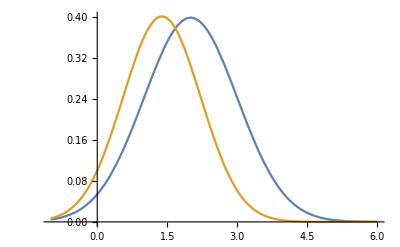

```mathematica
Plot[{PDF[NormalDistribution[2,1],x],7PDF[NormalDistribution[2,1],x]*PDF[NormalDistribution[0,1.5],x]},{x,-1,6}]
```

```mathematica
Manipulate[Plot[{PDF[NormalDistribution[g,1/(√n)],x],PDF[NormalDistribution[g,1/(√n)],x]PDF[NormalDistribution[0,√((k-1)/n)],x]},{x,-1,6}, PlotRange->Full],{g,0.1,1},{n ,1,10,1},{k,2,n}]
```

```mathematica
∫_(-∞)^g (g-x)^2 PDF[NormalDistribution[0,√(α/n)],x]PDF[NormalDistribution[0,1/(√n)],x - g]ⅆx
```

ConditionalExpression[1/(4 n^(3/2) π √(α/n) √((g^2 n α)/(1+α)) (1+α)^(7/2) √((g^2 n)/(α+α^2)))ⅇ^(-(g^2 n)/(2 α)) ((2 ⅇ^((g^2 n)/(2 α+2 α^2)) g^4 n^(5/2) α^(5/2) (1+α) √((g^2 n)/(α+α^2)) Erf[(g √n √(α/(1+α)))/(√2)])/(√((g^2 n α)/(2 π+2 π α)))+√(1+α) (-2 ⅇ^((g^2 n)/(2 α+2 α^2)) g^3 n^2 √(2 π) α^2 (1+α) √((g^2 n)/(α+α^2)) Erf[√((g^2 n α)/(2+2 α))]+√((g^2 n α)/(1+α)) (α √((g^2 n)/(α+α^2)) (ⅇ^((g^2 n)/(2 α+2 α^2)) g^2 n √(2 π) √(n (1+1/α))+2 g n (1+α)+ⅇ^((g^2 n)/(2 α+2 α^2)) √(2 π) √(n (1+1/α)) α (1+α))+ⅇ^((g^2 n)/(2 α+2 α^2)) g n √(2 π) (g^2 n+α+α^2) Erf[√((g^2 n)/(2 α+2 α^2))]))),(Re[g n]<0&&Re[n (1+1/α)]≥0)||Re[n (1+1/α)]>0]

```mathematica
Simplify[1/(4 n^(3/2) π √(α/n) √((g^2 n α)/(1+α)) (1+α)^(7/2) √((g^2 n)/(α+α^2)))ⅇ^(-(g^2 n)/(2 α)) ((2 ⅇ^((g^2 n)/(2 α+2 α^2)) g^4 n^(5/2) α^(5/2) (1+α) √((g^2 n)/(α+α^2)) Erf[(g √n √(α/(1+α)))/(√2)])/(√((g^2 n α)/(2 π+2 π α)))+√(1+α) (-2 ⅇ^((g^2 n)/(2 α+2 α^2)) g^3 n^2 √(2 π) α^2 (1+α) √((g^2 n)/(α+α^2)) Erf[√((g^2 n α)/(2+2 α))]+√((g^2 n α)/(1+α)) (α √((g^2 n)/(α+α^2)) (ⅇ^((g^2 n)/(2 α+2 α^2)) g^2 n √(2 π) √(n (1+1/α))+2 g n (1+α)+ⅇ^((g^2 n)/(2 α+2 α^2)) √(2 π) √(n (1+1/α)) α (1+α))+ⅇ^((g^2 n)/(2 α+2 α^2)) g n √(2 π) (g^2 n+α+α^2) Erf[√((g^2 n)/(2 α+2 α^2))]))) ,n > 0 && α > 1 && g > 0] // Cancel
```

1/(4 n^2 π √α (1+α)^(5/2))ⅇ^(-(g^2 n)/(2 α)) (2 g n α √(n/(α (1+α))) √((n α)/(1+α)) √(1+α)+2 g n α^2 √(n/(α (1+α))) √((n α)/(1+α)) √(1+α)+ⅇ^((g^2 n)/(2 α+2 α^2)) g^2 n √(2 π) α √(n/(α (1+α))) √((n α)/(1+α)) √(1+α) √((n (1+α))/α)+ⅇ^((g^2 n)/(2 α+2 α^2)) √(2 π) α √(n/(α (1+α))) √((n α)/(1+α)) √(1+α) √(n α (1+α)^3)+2 ⅇ^((g^2 n)/(2 α+2 α^2)) g^2 n^2 √(2 π) α √(n α) Erf[(g √((n α)/(1+α)))/(√2)]+2 ⅇ^((g^2 n)/(2 α+2 α^2)) g^2 n^2 √(2 π) α^2 √(n α) Erf[(g √((n α)/(1+α)))/(√2)]-2 ⅇ^((g^2 n)/(2 α+2 α^2)) g^2 n^(5/2) √(2 π) α √(1+α) √(α (1+α)) Erf[g √((n α)/(2+2 α))]+ⅇ^((g^2 n)/(2 α+2 α^2)) g^2 n^2 √(2 π) √((n α)/(1+α)) √(1+α) Erf[g √(n/(2 α+2 α^2))]+ⅇ^((g^2 n)/(2 α+2 α^2)) n √(2 π) α √((n α)/(1+α)) √(1+α) Erf[g √(n/(2 α+2 α^2))]+ⅇ^((g^2 n)/(2 α+2 α^2)) n √(2 π) α^2 √((n α)/(1+α)) √(1+α) Erf[g √(n/(2 α+2 α^2))])

```mathematica
PDF[NormalDistribution[0,√(α/n)],x]
```

(ⅇ^(-(n x^2)/(2 α)))/(√(2 π) √(α/n))

```mathematica
p[a_,b_,t_]:= a/(√(2π)t^(3/2))ⅇ^(-1/(2t)(a + b t)^2)
```

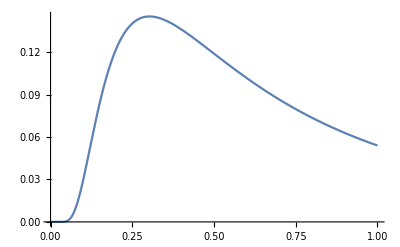

```mathematica
Plot[p[1,1,t],{t,0,1}]
```

```mathematica
Table[Table[p[a,n,1/n],{n,3,10}],{a,1,3}]//N
```

{{0.00513837,0.00107064,0.000202498,0.0000360249,6.14376×10^-6,1.01586×10^-6,1.64049×10^-7,2.60028×10^-8},{5.6839×10^-6,9.72141×10^-8,1.50928×10^-9,2.20402×10^-11,3.0854×10^-13,4.18768×10^-15,5.55108×10^-17,7.22251×10^-19},{2.34772×10^-10,1.21255×10^-13,5.68469×10^-17,2.50682×10^-20,1.05971×10^-23,4.3433×10^-27,1.73857×10^-30,6.83082×10^-34}}

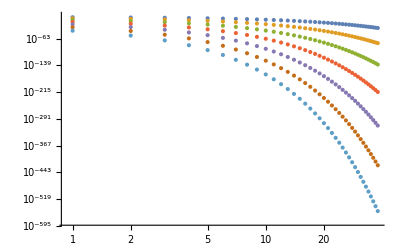

```mathematica
ListLogLogPlot[Table[Table[p[a,n,1/n],{n,3,40}],{a,1,7}]]
```

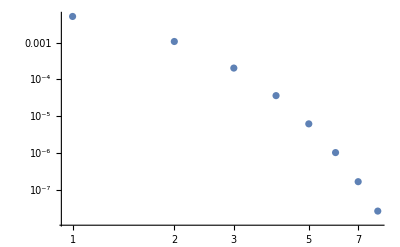

```mathematica
ListLogLogPlot[Table[p[1,n,1/n],{n,3,10}]]
```